```mathematica
<<NC`
<<NCAlgebra`
```

You are using the version of NCAlgebra which is found in:

/Users/mauricio/NC/

You can now use "<< NCAlgebra`" to load NCAlgebra.

```mathematica
<<NCPoly`
<<NCPolyGroebner`
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Options:

> VerboseLevel         -> 5

> SortBasis            -> False

> SimplifyObstructions -> True

> SortObstructions     -> False

> PrintObstructions    -> False

> PrintBasis           -> False

> PrintSPolynomials    -> False

* Monomial order: A<B

> G(0) = {A.B.A,-B}
{B.A.B,-B}

* Reduce and normalize initial set

> Initial set could not be reduced

> G(0) = {A.B.A,-B}
{B.A.B,-B}

* Initializing G tree

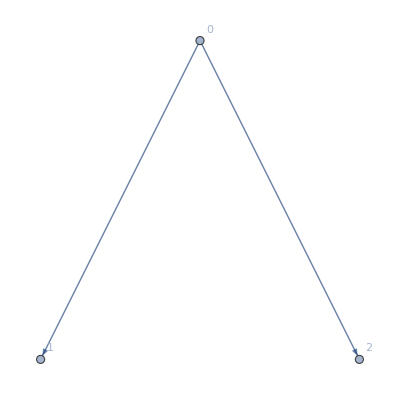
> GTree = -Graphics-

* Extracting leading monomials

> TG(0) = {{A.B.A},{B.A.B}}

* Computing initial set of obstructions

* Removing obstructions ({1, 1}) from set of obstructions

- Minor Iteration 1, 2 polys in the basis, 3 obstructions

* Selecting obstruction OBS(1,2)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {}

> h = {-B.B,B.A}

> q = {}

* S-Polynomial added to current basis

* Added node to GTree

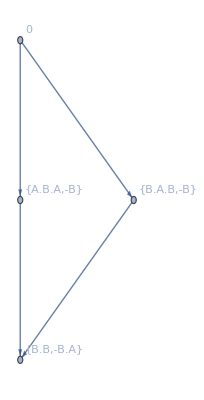
* GTree = -Graphics-

* GNodes = {1,2,3}

* Acyclic? = True

* ij = {1,2}

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 2, 3 polys in the basis, 5 obstructions

* Selecting obstruction OBS(1,2)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {3}

> h = {-B.A,A.B}

> q = {{{{-1,1,1}},3}}

> ij = {3}

> h = {-B.A,A.B}

> q = {}

> 2 polys in the current base can be reduced by S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

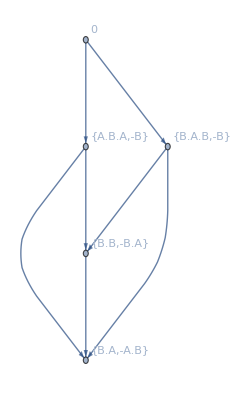
* GTree = -Graphics-

* GNodes = {1,2,3,4}

* Acyclic? = True

* ij = {1,2,3}

* Simplify current set of obstructions

* Removing obstructions ({2, 2}) from set of obstructions

* Removing obstructions ({2, 3}) from set of obstructions

* Computing new set of obstructions

* Reducing current base

> Reducing current base poly 1

> ij = {3}

> h = {A.A.B,-B}

> q = {{{{1,{A},1}},3}}

> ij = {3}

> h = {A.A.B,-B}

> q = {}

* Node contains 0

> Poly 1 does not reduce to zero; remainder added to base

* S-Polynomial added to current basis

* Added node to GTree

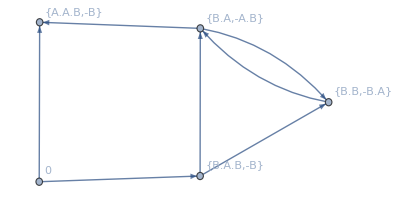
* GTree = -Graphics-

* GNodes = {1,2,3,4}

* Acyclic? = False

* ij = {3,0}

* Simplify current set of obstructions

* Computing new set of obstructions

* Replaced at GTree

* GTree = -Graphics-

* GNodes = {1,2,3,4}

* Acyclic? = False

> Reducing current base poly 1

> ij = {1,2,3}

> h = 0

> q = {{{{1,1,{B}}},2},{{{1,{A},1}},1},{{{1,{A},1}},2},{{{1,1,1}},3}}

* Node contains 0

* Removed from GTree

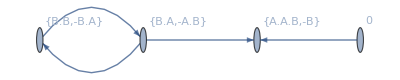
* GTree = -Graphics-

* GNodes = {1,2,3}

* Acyclic? = False

> Poly 1 reduced to zero; removing from base

- Minor Iteration 3, 3 polys in the basis, 5 obstructions

> MAJOR Iteration 1, 3 polys in the basis, 5 obstructions

* Selecting obstruction OBS(1,1)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {1,2}

> h = 0

> q = {{{{-1,1,{A}}},1},{{{1,1,{B}},{-1,1,{A}}},2},{{{1,{A},1}},1}}

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 4, 3 polys in the basis, 4 obstructions

* Selecting obstruction OBS(1,2)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {1,2}

> h = 0

> q = {{{{1,1,{B}},{-1,1,{A}}},2},{{{1,{A},1}},1}}

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 5, 3 polys in the basis, 3 obstructions

* Selecting obstruction OBS(1,3)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {1,2,3}

> h = 0

> q = {{{{-1,{A.A},1}},2},{{{-1,{A},1}},3},{{{1,1,1}},1},{{{1,1,1}},2}}

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 6, 3 polys in the basis, 2 obstructions

* Selecting obstruction OBS(2,3)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {1,2,3}

> h = 0

> q = {{{{-1,{A},{B}}},2},{{{-1,{A.A},1}},1},{{{-1,{A.A},1}},2},{{{-1,{A},1}},3},{{{1,1,1}},1},{{{1,1,1}},2}}

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 7, 3 polys in the basis, 1 obstructions

* Selecting obstruction OBS(2,3)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {2,3}

> h = 0

> q = {{{{-1,{A},1}},3},{{{1,1,1}},2}}

* S-Polynomial was completely reduced and has been removed from the set of obstructions

* Found Groebner basis with 3 polynomials

* * * * * * * * * * * * * * * *

{{b.b,-b.a},{b.a,-a.b},{a.a.b,-b}}

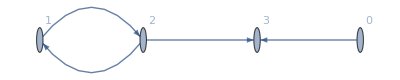

```mathematica
vars={a,b};
g1=NCPolyMonomial[{a,b,a},vars]-NCPolyMonomial[{b},vars];
g2=NCPolyMonomial[{b,a,b},vars]-NCPolyMonomial[{b},vars];

g={g1,g2};
{G,graph}=NCPolyGroebner[g,12,VerboseLevel->5];
NCPolyDisplay[G,vars]
Graph[graph,VertexLabels->"Name"]
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Options:

> VerboseLevel         -> 4

> SortBasis            -> False

> SimplifyObstructions -> True

> SortObstructions     -> False

> PrintObstructions    -> False

> PrintBasis           -> False

> PrintSPolynomials    -> False

* Monomial order: A<B

> G(0) = {B.B,-B}
{B.A.B,-A.B}

* Reduce and normalize initial set

> Initial set could not be reduced

> G(0) = {B.B,-B}
{B.A.B,-A.B}

* Initializing G tree

> GTree = -Graphics-

* Extracting leading monomials

> TG(0) = {{B.B},{B.A.B}}

* Computing initial set of obstructions

- Minor Iteration 1, 2 polys in the basis, 4 obstructions

* Selecting obstruction OBS(1,1)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 2, 2 polys in the basis, 3 obstructions

* Selecting obstruction OBS(1,2)

* Building S-Polynomial

> Zero S-Polynomial!

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 3, 2 polys in the basis, 2 obstructions

* Selecting obstruction OBS(1,2)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 4, 2 polys in the basis, 1 obstructions

* Selecting obstruction OBS(2,2)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

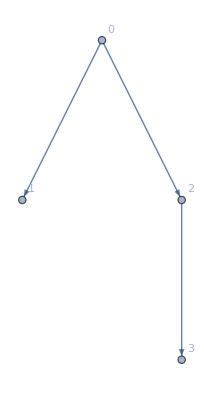
* GTree = -Graphics-

* GNodes = {1,2,3}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 5, 3 polys in the basis, 5 obstructions

> MAJOR Iteration 1, 3 polys in the basis, 5 obstructions

* Selecting obstruction OBS(1,3)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 6, 3 polys in the basis, 4 obstructions

* Selecting obstruction OBS(1,3)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 7, 3 polys in the basis, 3 obstructions

* Selecting obstruction OBS(2,3)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

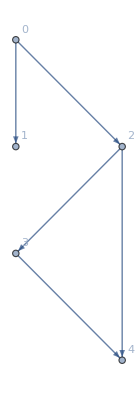
* GTree = -Graphics-

* GNodes = {1,2,3,4}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 8, 4 polys in the basis, 9 obstructions

* Selecting obstruction OBS(2,3)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 9, 4 polys in the basis, 8 obstructions

* Selecting obstruction OBS(3,3)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

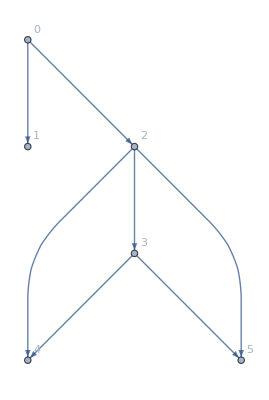
* GTree = -Graphics-

* GNodes = {1,2,3,4,5}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 10, 5 polys in the basis, 16 obstructions

> MAJOR Iteration 2, 5 polys in the basis, 16 obstructions

* Selecting obstruction OBS(1,4)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 11, 5 polys in the basis, 15 obstructions

* Selecting obstruction OBS(1,4)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 12, 5 polys in the basis, 14 obstructions

* Selecting obstruction OBS(2,4)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 13, 5 polys in the basis, 13 obstructions

* Selecting obstruction OBS(2,4)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 14, 5 polys in the basis, 12 obstructions

* Selecting obstruction OBS(3,4)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

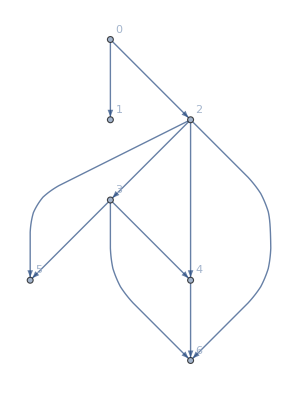
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 15, 6 polys in the basis, 22 obstructions

* Selecting obstruction OBS(3,4)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 16, 6 polys in the basis, 21 obstructions

* Selecting obstruction OBS(4,4)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

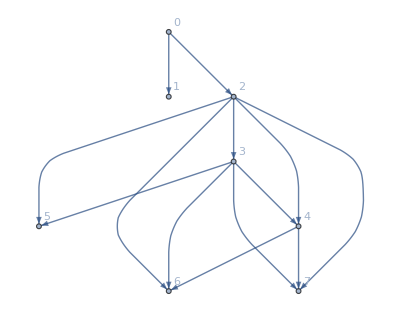
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 17, 7 polys in the basis, 33 obstructions

* Selecting obstruction OBS(1,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 18, 7 polys in the basis, 32 obstructions

* Selecting obstruction OBS(1,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 19, 7 polys in the basis, 31 obstructions

* Selecting obstruction OBS(2,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 20, 7 polys in the basis, 30 obstructions

* Selecting obstruction OBS(2,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 21, 7 polys in the basis, 29 obstructions

* Selecting obstruction OBS(3,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 22, 7 polys in the basis, 28 obstructions

* Selecting obstruction OBS(3,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 23, 7 polys in the basis, 27 obstructions

* Selecting obstruction OBS(4,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

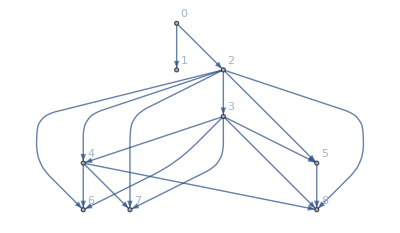
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 24, 8 polys in the basis, 41 obstructions

* Selecting obstruction OBS(4,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 25, 8 polys in the basis, 40 obstructions

* Selecting obstruction OBS(5,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

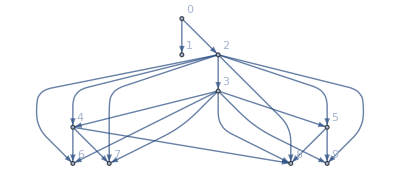
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7,8,9}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 26, 9 polys in the basis, 56 obstructions

> MAJOR Iteration 3, 9 polys in the basis, 56 obstructions

* Cleaning up...

* Reducing 1 basis entry

* Reducing 2 basis entry

* Reducing 3 basis entry

* Reducing 4 basis entry

* Reducing 5 basis entry

* Reducing 6 basis entry

* Reducing 7 basis entry

* Reducing 8 basis entry

* Reducing 9 basis entry

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 9 polynomials

* * * * * * * * * * * * * * * *

{{p.p,-p},{p.a.p,-a.p},{p.a.a.p,-a.p.a.p},{p.a.a.a.p,-a.p.a.a.p},{p.a.a.a.a.p,-a.a.p.a.a.p},{p.a.a.a.a.a.p,-a.a.p.a.a.a.p},{p.a.a.a.a.a.a.p,-a.a.a.p.a.a.a.p},{p.a.a.a.a.a.a.a.p,-a.a.a.p.a.a.a.a.p},{p.a.a.a.a.a.a.a.a.p,-a.a.a.a.p.a.a.a.a.p}}

-Graphics-

```mathematica
Clear[a,p];
vars={a,p};

g={
NCPolyMonomial[{p,p},vars]-NCPolyMonomial[{p},vars],NCPolyMonomial[{p,a,p},vars]-NCPolyMonomial[{a,p},vars]};

{G,graph}=NCPolyGroebner[g,3,VerboseLevel->4, CleanUpBasis->True];
NCPolyDisplay[G,vars]
Graph[graph,VertexLabels->"Name"]
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Options:

> VerboseLevel         -> 4

> SortBasis            -> False

> SimplifyObstructions -> True

> SortObstructions     -> False

> PrintObstructions    -> False

> PrintBasis           -> False

> PrintSPolynomials    -> False

* Monomial order: A<B<C

> G(0) = {C.C,-A}
{C.C.C,-B}

* Reduce and normalize initial set

> Initial set could not be reduced

> G(0) = {C.C,-A}
{A.C,-B}

* Initializing G tree

> GTree = -Graphics-

* Extracting leading monomials

> TG(0) = {{C.C},{A.C}}

* Computing initial set of obstructions

- Minor Iteration 1, 2 polys in the basis, 2 obstructions

* Selecting obstruction OBS(1,1)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

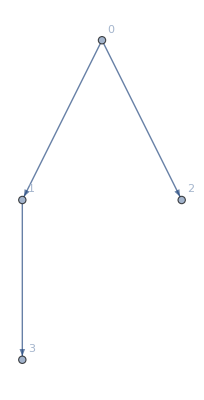
* GTree = -Graphics-

* GNodes = {1,2,3}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 2, 3 polys in the basis, 4 obstructions

* Selecting obstruction OBS(1,2)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

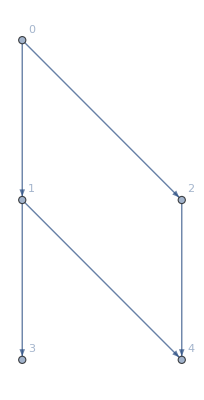
* GTree = -Graphics-

* GNodes = {1,2,3,4}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 3, 4 polys in the basis, 5 obstructions

> MAJOR Iteration 1, 4 polys in the basis, 5 obstructions

* Selecting obstruction OBS(1,3)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

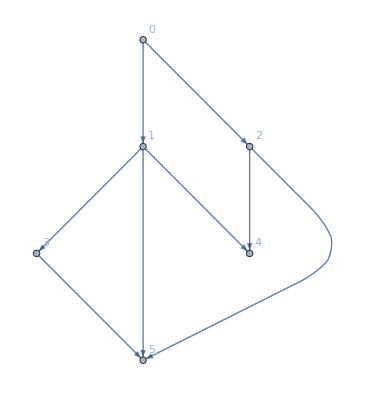
* GTree = -Graphics-

* GNodes = {1,2,3,4,5}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 4, 5 polys in the basis, 8 obstructions

* Selecting obstruction OBS(2,3)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 5, 5 polys in the basis, 7 obstructions

* Selecting obstruction OBS(2,3)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

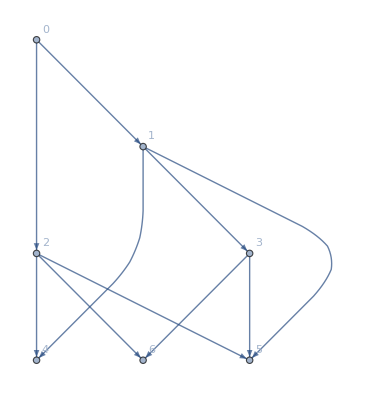
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 6, 6 polys in the basis, 8 obstructions

* Selecting obstruction OBS(1,4)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 7, 6 polys in the basis, 7 obstructions

* Selecting obstruction OBS(3,4)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

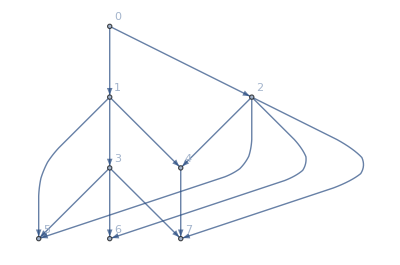
* GTree = -Graphics-

* GNodes = {1,2,3,4,5,6,7}

* Acyclic? = True

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

- Minor Iteration 8, 7 polys in the basis, 10 obstructions

> MAJOR Iteration 2, 7 polys in the basis, 10 obstructions

* Selecting obstruction OBS(1,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 9, 7 polys in the basis, 9 obstructions

* Selecting obstruction OBS(2,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 10, 7 polys in the basis, 8 obstructions

* Selecting obstruction OBS(4,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 11, 7 polys in the basis, 7 obstructions

* Selecting obstruction OBS(4,5)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 12, 7 polys in the basis, 6 obstructions

* Selecting obstruction OBS(2,6)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 13, 7 polys in the basis, 5 obstructions

* Selecting obstruction OBS(5,6)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 14, 7 polys in the basis, 4 obstructions

* Selecting obstruction OBS(2,7)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 15, 7 polys in the basis, 3 obstructions

* Selecting obstruction OBS(3,7)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 16, 7 polys in the basis, 2 obstructions

* Selecting obstruction OBS(6,7)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 17, 7 polys in the basis, 1 obstructions

* Selecting obstruction OBS(7,7)

* Building S-Polynomial

* Reducing S-Polynomial

* S-Polynomial was completely reduced and has been removed from the set of obstructions

* Cleaning up...

* Reducing 1 basis entry

* Reducing 2 basis entry

* Reducing 3 basis entry

* Reducing 4 basis entry

* Reducing 5 basis entry

* Reducing 6 basis entry

* Reducing 7 basis entry

* Found Groebner basis with 7 polynomials

* * * * * * * * * * * * * * * *

{{x.x,-a},{a.x,-b},{x.a,-a.x},{b.x,-a.a},{x.b,-a.a},{b.a,-a.b},{a.a.a,-b.b}}

-Graphics-

```mathematica
Clear[a,b,x];
vars={a,b,x};

g={
NCPolyMonomial[{x,x},vars]-NCPolyMonomial[{a},vars],NCPolyMonomial[{x,x,x},vars]-NCPolyMonomial[{b},vars]};

{G,graph}=NCPolyGroebner[g,3,VerboseLevel->4,CleanUpBasis->True];
NCPolyDisplay[G,vars]
Graph[graph,VertexLabels->"Name"]
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Options:

> VerboseLevel         -> 5

> SortBasis            -> False

> SimplifyObstructions -> True

> SortObstructions     -> False

> PrintObstructions    -> False

> PrintBasis           -> False

> PrintSPolynomials    -> False

* Monomial order: A<B≪ C<D

> G(0) = {A.B.C.D,-1}
{-B.A,A.B}
{-C.B.A,A.B.C}
{C.B.A,-C}
{C,B}

* Reduce and normalize initial set

> Initial set reduced to '4' out of '5' polynomials

> G(0) = {B.D,1}
{B.A,-A.B}
{A.B.B,-B}
{C,B}

* Initializing G tree

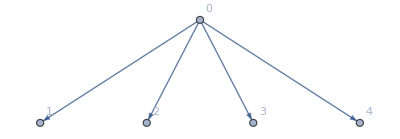
> GTree = -Graphics-

* Extracting leading monomials

> TG(0) = {{B.D},{B.A},{A.B.B},{C}}

* Computing initial set of obstructions

- Minor Iteration 1, 4 polys in the basis, 3 obstructions

* Selecting obstruction OBS(1,3)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {1}

> h = {A.B,-1}

> q = {{{{1,1,1}},1}}

> ij = {1}

> h = {A.B,-1}

> q = {}

> 1 polys in the current base can be reduced by S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

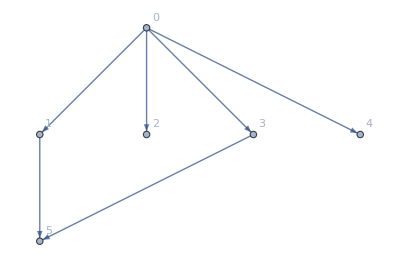
* GTree = -Graphics-

* GNodes = {1,2,3,4,5}

* Acyclic? = True

* ij = {1,3}

* Simplify current set of obstructions

* Removing obstructions ({2, 3}) from set of obstructions

* Computing new set of obstructions

* Reducing current base

> Reducing current base poly 3

> ij = {4}

> h = 0

> q = {{{{1,1,{B}}},4}}

* Node contains 0

* Removed from GTree

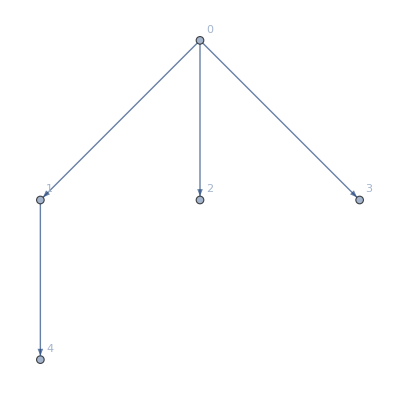
* GTree = -Graphics-

* GNodes = {1,2,3,4}

* Acyclic? = True

> Poly 3 reduced to zero; removing from base

- Minor Iteration 2, 4 polys in the basis, 3 obstructions

> MAJOR Iteration 1, 4 polys in the basis, 3 obstructions

* Selecting obstruction OBS(1,4)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {}

> h = {D,A}

> q = {}

> 1 polys in the current base can be reduced by S-Polynomial

* S-Polynomial added to current basis

* Added node to GTree

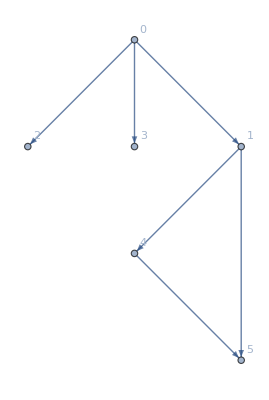
* GTree = -Graphics-

* GNodes = {1,2,3,4,5}

* Acyclic? = True

* ij = {1,4}

* Simplify current set of obstructions

* Computing new set of obstructions

* Reducing current base

> Reducing current base poly 1

> ij = {1,3,4}

> h = 0

> q = {{{{1,{B},1}},4},{{{-1,1,1}},1},{{{-1,1,1}},3}}

* Node contains 0

* Removed from GTree

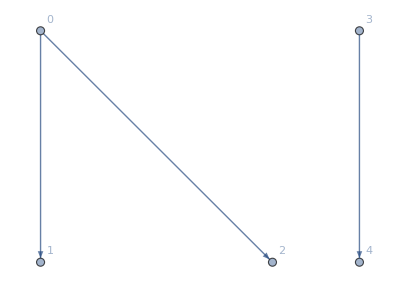
* GTree = -Graphics-

* GNodes = {1,2,3,4}

* Acyclic? = True

> Poly 1 reduced to zero; removing from base

- Minor Iteration 3, 4 polys in the basis, 2 obstructions

* Selecting obstruction OBS(1,3)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {3}

> h = 0

> q = {{{{-1,{A},1}},3}}

* S-Polynomial was completely reduced and has been removed from the set of obstructions

- Minor Iteration 4, 4 polys in the basis, 1 obstructions

* Selecting obstruction OBS(1,3)

* Building S-Polynomial

* Reducing S-Polynomial

> ij = {3}

> h = 0

> q = {{{{-1,1,{B}}},3}}

* S-Polynomial was completely reduced and has been removed from the set of obstructions

* Cleaning up...

* Reducing 1 basis entry

* Reducing 2 basis entry

* Reducing 3 basis entry

* Reducing 4 basis entry

* Found Groebner basis with 4 polynomials

* * * * * * * * * * * * * * * *

{{B.A,-A.B},{c,B},{A.B,-1},{d,A}}

-Graphics-

```mathematica
Clear[A,B,c,d];
SetNonCommutative[A,B,c,d];
vars={{A,B},{c,d}};

rels=NCToNCPoly[{A**B**c**d-1,A**B-B**A,A**B**c-c**B**A,c**B**A-c,c+B},vars];

{G,graph}=NCPolyGroebner[rels,4,VerboseLevel->5,CleanUpBasis->True];
NCPolyDisplay[G,vars]
Graph[graph,VertexLabels->"Name"]
```

```mathematica
?*VertexIn*
```

RowBox[{"VertexInDegree", "[", StyleBox["g", "TI"], "]"}] gives the list of vertex in-degrees for all vertices in the graph StyleBox["g", "TI"].
RowBox[{"VertexInDegree", "[", RowBox[{StyleBox["g", "TI"], ",", StyleBox["v", "TI"]}], "]"}] gives the vertex in-degree for the vertex StyleBox["v", "TI"].
RowBox[{"VertexInDegree", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}], ",", StyleBox["…", "TR"]}], "}"}], ",", "…"}], "]"}] uses rules RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}] to specify the graph StyleBox["g", "TI"].

```mathematica
Pick[{a,b,c},{0,1,2},_?(#≤1&)]
```

{a,b}